```mathematica
`
```

## MICA: Measurement, Instrumentation, Control and Analysis

## Sallen-Key Filter System ID

#### Ariel Mobius, MIT 12 March 2026

-Graphics-

#### Revisions

2021		Sep	30	Started
2023		Dec	04 	Updated to use the Digilent Discovery 3
2024		Mar	11	Many improvements
2025		Mar	05	Updated to use modified PCB
			11	Made a few corrections
		Oct	13	Updated and changed capacitors to 15 nF and resistors to 10 kΩ
			14	Added measured step response prediction
			15	Added measured white stochastic response prediction
2026		Mar	04	Updated
			11	Added parameter sensitivity functions and mean square error display

#### Keywords

Frequency Response, Transfer Function, Laplace Transform, Inverse Laplace Transform, Bode Plot, Gain, Phase, Filter, System ID, Sallen-Key Filter, Low-Pass System, High-Pass System, Second-Order System, Gain, Natural Frequency, Damping Parameter, Hertz (Hz), Radians/s, Impulse Response Function, Resistor, Capacitor, Inductor, Step Response, Electrical Impedance, Minimization, Objective Function, Parameter Estimation, Least-Squares, Levenberg-Marquardt Algorithm, Step Response, Network Analyzer, Swept Sine, Stochastic Input, Stochastic Response, Convolution, Prediction Error, Variance Accounted For (VAF), Parametric Model, Non-Parametric Model, Mean Square Error (MSE), Parameter Sensitivity Functions

#### Objectives

In the following we use the Network Analyzer capability of the Digilent Discovery 3 and Digilent Waveforms software to measure the frequency response of a second-order low-pass filter. The particular circuit used here to implement the filter is called a Sallen-Key filter and is elegant in that second-order low-pass or high-pass filters are implemented using a single operational amplifier (op amp) and two resistors (10 kΩ) and two capacitors (15 nF). 

The sinusoidal signal delivered to the input of the Sallen-Key filter is generated by the Discovery Waveform 1 output. A copy of this Sallen-Key filter input is sent to the Discovery Scope Channel 1. This is considered to the input to the system (i.e. the Sallen-Key filter being tested). 

The output from the Sallen-Key filter is sent to the Discovery Scope Channel 2 and is considered to be the output of the system (i.e. the Sallen-Key filter). 

The Waveforms Network Analyzer measures the frequency response between the system input and output under test using sinusoidal inputs of different frequencies (swept from low frequencies to high frequencies). High-end commercial Network Analyzers (sometimes called Dynamic Analyzers) often provide a variety of different types of inputs including swept sinusoids,  chirps, Gaussian white noise, binary white noise. Such high-end instruments might do auto-ranging of both input and output and allow for more samples to be taken around rapidly changing peaks (adaptive system id).

The Waveforms Network Analyzer has a wide range of options including the ability to display the measurements in real-time as a Bode plot (and others such as Nyquist and Nichols plots).

◦	 DAC resolution is ~0.7 mV for amplitudes above 1 V, and ~0.18 mV for amplitudes of 1 V and lower

#### Connect Sallen-Key filter to Discovery 3

Connect Red wire from the Discovery V+ Power Supply (must be set to +5 V and enabled) to the PCB V+
Connect White wire from the Discovery V- Power Supply (must be set to -5 V and enabled) to the PCB V- 
Connect Black wire (any will do) from the Discovery to the PCB power supply GND (the pin is between V+ and V-)
Connect Yellow wire from the Discovery Waveform Generator 1 to the PCB Vin
Connect Orange wire from the Discovery Scope Channel 1 Positive to the PCB Vin
Connect Orange/White wire from the Discovery Scope Channel 1 Negative input to the PCB Vin GND
Connect Blue wire from the Discovery Scope Channel 2 Positive input to the PCB Vout
Connect Blue/White wire from the Discovery Scope Channel 2 Negative input to the PCB Vout GND
Note that both the Discovery Waveform Generator (Yellow wire) and the Discovery Scope Channel 1 Positive (Orange wire) need to be connected to the PCB Vin. Use  patch cables and a 3 pin shunt (shorting connector) for this.

This pinout diagram might help:

-Graphics-

#### Turn on power supply

The Sallen-Key filter requires both a positive and a negative power supply. The Discovery 3 has both a positive and a negative power supply which by default are set to +1 V and -1 V are are off (not enabled). Set the power supply values to +5 V and -5 V and turn them on (Master Enable is On).

-Graphics-

#### Set up the Network Analyzer

By default the Network Analyzer sweeps a 1 V amplitude sinusoidal input from 1 kHz to 1 MHz. Our Sallen-Key filter is really designed to work over audio frequencies (i.e., human range of 20 Hz to 20 kHz). So change the Start and Stop frequencies to run from 10 Hz to 100 kHz. Also increase the sinusoidal input amplitude (Amplitude) to 2V (as shown below).

By default the Network Analyzer displays the Magnitude part of the Bode plot using dB units. Change to gain (X) and then change from Linear to Logarithmic axis (click on the Magnitude setting icon to do this). Set the Magnitude to: Top: 2 X and Bottom: 0.0001 X (100 uX).
Change the Phase part of the Bode plot to the values shown below (Offset -90 ° and Range 240 °).
After generating the Bode plot you can un-click Channel 1 to remove the yellow/orange trace (you might have to re-click it in order to generate another Bode plot).

-Graphics-

#### Measure the Frequency Response and Save

Acquire a single sweep (use Single rather than Run) and then Export (i.e., save) the frequency response as follows:

-Graphics-

-Graphics-

Click on File then Export then Save to save to a .csv file on your Downloads folder called: Sallen-Key Filter Frequency Response

#### Import the Measured Frequency Response in to Mathematica

You will need to change the file name below to the location where you saved the measured frequency response.

```mathematica
"■";  
file=
"C:\Users\ariel\Downloads\Sallen-Key Filter Frequency Response ariel.csv";
data=Import[file,"Data"][[1;;31]]  (* header info *)
```

{{#Digilent WaveForms Network Analyzer - Bode},{#Device Name: Discovery3},{#Serial Number: SN:210415BE8CFA},{#Date Time: 2026-03-17 19:13:35.669},{#Start: 10 Hz},{#Stop: 100000 Hz},{#Steps: 151},{#Wavegen: Wavegen C1},{#Amplification: 1 X},{#Settle: 10 ms},{#MinPeriods: 16},{#Channel: Channel 2},{#Range: 5.15214 V},{#Offset: -0.000265344 V},{#Relative: yes},{#Power Supplies: ON},{#Positive Supply: ON},{#Voltage: 5 V Readback: 5.000659852 V},{#Negative Supply: ON},{#Voltage: -5 V Readback: -4.9987029675 V},{Frequency (Hz),Channel 2 Magnitude (X),Channel 2 Phase (deg)},{10,0.999831,-1.13137},{10.6333,0.999789,-1.20313},{11.3066,0.999773,-1.27917},{12.0226,0.999772,-1.35973},{12.784,0.999721,-1.44577},{13.5936,0.999676,-1.5365},{14.4544,0.999639,-1.6333},{15.3697,0.999597,-1.73657},{16.3431,0.999545,-1.84621},{17.378,0.99948,-1.96277}}

Check first triplet of data (i.e., at 10 Hz) is at CSV row 22 (note that yours may be at another line number):

```mathematica
"■"; Import[file,"Data"][[22]]
```

{10,0.999831,-1.13137}

```mathematica
"■"; data=Import[file,"Data"][[22;;All]] ;(* data starts at element 23 *)
n=Length[data]
```

151

This length should be the same as the number of samples collected by WaveForms (e.g., 151).

```mathematica
"■"; freq=data[[All,1]];
gain=data[[All,2]];
phase=data[[All,3]];
```

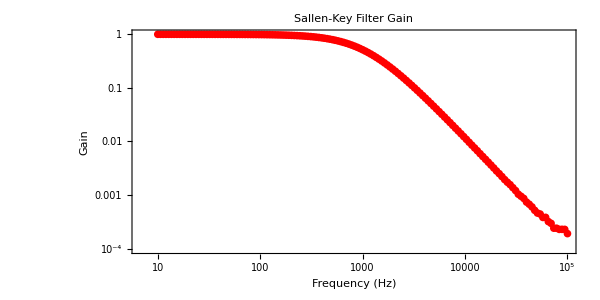

```mathematica
"■"; ListLogLogPlot[{freq,gain}ᵀ,PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Gain",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImageSize->600]
```

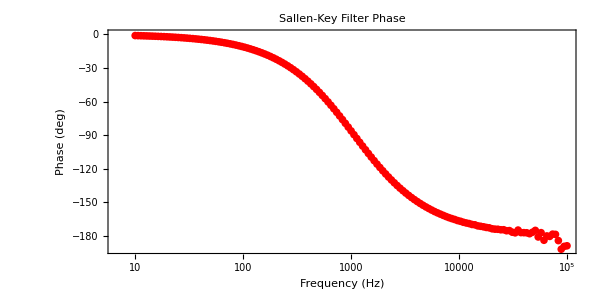

```mathematica
"■"; ListLogLinearPlot[{freq,phase}ᵀ,PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Phase",
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImageSize->600]
```

Note that the variation in gain and phase measurements at high frequencies occurs because at these high frequencies the output sinusoidal amplitude is very small and likely near the resolution of the 16 bit ADCs used in the Digilent Discovery 3. For example with the 2 V amplitude input sinusoid at 100 kHz the output sinusoidal amplitude will be around 2 10^-4 V = 0.2 mV. 
The Digilent Discovery 3 two ADCs are 14 bit but below 50 MHz sampling rates (as used here) act as 16 bit ADCs. Each of the ADCs  has a range of ± 25 V or ± 2.5 V. Assuming that the larger voltage range is used by the Network Analyzer then this means that the smallest voltage is  (±25 V)/2^16 = 0.00076 V = 0.076 mV. So 0.2 mV is only 3 times large than the minimum bit resolution of the ADC. ADCs typically have at least 1/2 bit of noise so the 0.2 mV is almost at the noise limit of the Network Analyzer. High end Network Analyzer (sometimes call Dynamic Analyzers or Gain-Phase Analyzer) can cost 100 k$ but often include a mechanism to automatically increase the gain of the output channel ADC when the sinusoidal response amplitude is very small so as to avoid this problem.

#### Consideration of Model Order

The high frequency roll-off gives a clue as to model order. When plotting on Log Log axes the Bode gain of a simple low-pass system should roll off with a slope equal to minus the system order. For example if the order is 2 then the high frequency asymptotic roll-off slope should be -2 (i.e. the high frequency system gain becomes 100 x less as the frequency in increased 10 x). The colored “roll-off” lines shown on the gain part of the Bode plot below have slopes of -1 (cyan), -2 (blue), and -3 (brown). The blue line is closest to the measured data and so we conclude that the system is second-order. This is confirmed by looking at the phase part of the Bode plot. The difference in value between the asymptotic low frequency phase value (0 deg here) and the asymptotic high frequency phase value will be -90 times the system order. In our case this phase difference is 180 deg which confirms that we have a second-order system. 

Note that the asymptotic low frequency phase value will be 180 deg rather than 0 deg if the overall static gain is negative. So in this case we can see that the overall gain of the Sallen-Key filter is positive because the low frequency phase starts at 0 and in addition it looks as though the value of the static gain, α, (i.e. its asymptotically low frequency gain value) is 1. This can be seen in the plot below.

The cutoff frequency, ω,  will occur when the phase is half way between the low and high frequency asymptotes (-90 here). In the plot below a vertical black line has been drawn through this half way point in the phase part of the Bode plot and extended up in to the gain part of the Bode plot. This line should intersect the black horizontal asymptotic low frequency gain line and the colored high frequency roll-off line extrapolated back to lower frequencies. See if this is indeed the case once the static gain, α, has been adjusted:

Manipulate[
 Column[{
  Show[
   ListLogLogPlot[{freq, gain}, PlotStyle -> Red], (* Measured *)
   LogLogPlot[Abs[H[I f 2 Pi, a, w, z]], {f, 10, 100000}, PlotStyle -> Black] (* Model *)
  ],
  Show[
   ListLogLinearPlot[{freq, phase}, PlotStyle -> Red], (* Measured *)
   LogLinearPlot[360/(2 Pi) Arg[H[I f 2 Pi, a, w, z]], {f, 10, 100000}, PlotStyle -> Black] (* Model *)
  ]
 }],
 {{a, 1.0, “a”}, 0.1, 2.0},
 {{w, 1000*2*Pi, “w (rad/s)”}, 100*2*Pi, 5000*2*Pi},
 {{z, 1.0, “zeta”}, 0.1, 2.0}
]

```mathematica
"■"; Manipulate[
cutoffFreq=InverseFunction[Interpolation[{freq,phase},InterpolationOrder->1]][-90];(* finds frequency at which interpolated phase is -90 deg *)
Column[
{
ListLogLogPlot[{
{freq,gain}ᵀ,
{{10,α},{20000,α}},
{{cutoffFreq,α},{100 cutoffFreq,0.01 α}},
{{cutoffFreq,α},{100 cutoffFreq,0.0001 α}},
{{cutoffFreq,α},{100 cutoffFreq,0.000001 α}},
{{cutoffFreq,0.0001},{cutoffFreq,2}}},
PlotRange->{{10, 100000},{0.0001,5}},
Frame->True,Joined->{False,True,True,True,True,True,True},PlotStyle->{Red,Black,Cyan,Blue,Brown,Black},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600,
Epilog->
{Black,Text[cutoffFreq "Hz",Scaled[{0.53,0.95}]],
Cyan,Text["-1" ,Scaled[{0.8,0.7}]],
Blue,Text["-2" ,Scaled[{0.66,0.7}]],
Brown,Text["-3" ,Scaled[{0.55,0.7}]]}],
ListLogLinearPlot[{
{freq,phase}ᵀ,
{{10,0},{10^5,0}},
{{10,-90},{10^5,-90}},
{{10,-180},{10^5,-180}},
{{cutoffFreq,-200},{cutoffFreq,10}}},
PlotRange->{{10, 100000},{-200,10}},
Frame->True,Joined->{False,True,True,True,True},
PlotStyle->{Red,{Black,Dashed},Black,{Black,Dashed},Black},LabelStyle->{14,Black},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600,
Epilog->
{Black,Text["-90 deg" ,Scaled[{0.1,0.56}]],
Black,Text["-180 deg" ,Scaled[{0.1,0.14}]]}]
},
Spacings->0],
{{α,0.5},0.1,2.0,0.1,Appearance->"Labeled"},
ControlPlacement->Top]
```

It can be seen that the cut-off frequency (natural frequency), ω, is a little above 1 kHz (or 2π 1000 rad/s).

A simple low-pass, second-order system is defined by three parameters: the static gain, α, the natural frequency, ω, and the damping parameter, ζ.  As yet we have not estimated the value of the damping parameter but from experience it looks as though it is somewhere around 1.

In the following we allow all three parameters to be adjusted to give a feel for the effect each has on the features of the Bode plot.

#### Fit a Parametric Second-Order Transfer Function Model by Hand

The general equation for the transfer function of a second-order low-pass filter is:

```mathematica
"■"; H[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2);
```

where the static gain is α, the natural frequency (in radians/s) is ω, and the damping parameter is ζ.

The error between the ith measured gain value and the model with parameters α,ω, and ζ is given by:

```mathematica
gain[[i]]-Abs[H[ⅈ freq[[i]] 2 π,α,ω,ζ]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

-Abs[(α ω^2)/(ω^2+4 ⅈ π ζ ω {10,10.6333,11.3066,12.0226,12.784,13.5936,14.4544,15.3697,16.3431,17.378,18.4785,19.6487,20.893,22.216,23.6229,25.1189,26.7096,28.401,30.1995,32.1119,34.1455,36.3078,38.6071,41.0519,43.6516,46.4159,49.3552,52.4807,55.8042,59.3381,63.0957,67.0914,71.34,75.8578,80.6616,85.7696,91.2011,96.9765,103.118,109.648,116.591,123.975,131.826,140.174,149.05,158.489,168.526,179.198,190.546,202.613,215.443,229.087,243.594,259.02,275.423,292.864,311.411,331.131,352.101,374.398,398.107,423.318,450.125,478.63,508.94,541.17,575.44,611.881,650.629,691.831,735.642,782.228,831.764,884.437,940.445,1000,1063.33,1130.66,1202.26,1278.4,1359.36,1445.44,1536.97,1634.31,1737.8,1847.85,1964.87,2089.3,2221.6,2362.29,2511.89,2670.96,2840.1,3019.95,3211.19,3414.55,3630.78,3860.71,4105.19,4365.16,4641.59,4935.52,5248.07,5580.42,5933.81,6309.57,6709.14,7134.,7585.78,8066.16,8576.96,9120.11,9697.65,10311.8,10964.8,11659.1,12397.5,13182.6,14017.4,14905.,15848.9,16852.6,17919.8,19054.6,20261.3,21544.3,22908.7,24359.4,25902.,27542.3,29286.4,31141.1,33113.1,35210.1,37439.8,39810.7,42331.8,45012.5,47863.,50894.,54117.,57544.,61188.1,65062.9,69183.1,73564.2,78222.8,83176.4,88443.7,94044.5,100000}⟦i⟧-4 π^2 ({10,10.6333,11.3066,12.0226,12.784,13.5936,14.4544,15.3697,16.3431,17.378,18.4785,19.6487,20.893,22.216,23.6229,25.1189,26.7096,28.401,30.1995,32.1119,34.1455,36.3078,38.6071,41.0519,43.6516,46.4159,49.3552,52.4807,55.8042,59.3381,63.0957,67.0914,71.34,75.8578,80.6616,85.7696,91.2011,96.9765,103.118,109.648,116.591,123.975,131.826,140.174,149.05,158.489,168.526,179.198,190.546,202.613,215.443,229.087,243.594,259.02,275.423,292.864,311.411,331.131,352.101,374.398,398.107,423.318,450.125,478.63,508.94,541.17,575.44,611.881,650.629,691.831,735.642,782.228,831.764,884.437,940.445,1000,1063.33,1130.66,1202.26,1278.4,1359.36,1445.44,1536.97,1634.31,1737.8,1847.85,1964.87,2089.3,2221.6,2362.29,2511.89,2670.96,2840.1,3019.95,3211.19,3414.55,3630.78,3860.71,4105.19,4365.16,4641.59,4935.52,5248.07,5580.42,5933.81,6309.57,6709.14,7134.,7585.78,8066.16,8576.96,9120.11,9697.65,10311.8,10964.8,11659.1,12397.5,13182.6,14017.4,14905.,15848.9,16852.6,17919.8,19054.6,20261.3,21544.3,22908.7,24359.4,25902.,27542.3,29286.4,31141.1,33113.1,35210.1,37439.8,39810.7,42331.8,45012.5,47863.,50894.,54117.,57544.,61188.1,65062.9,69183.1,73564.2,78222.8,83176.4,88443.7,94044.5,100000}⟦i⟧)^2)]+{0.999831,0.999789,0.999773,0.999772,0.999721,0.999676,0.999639,0.999597,0.999545,0.99948,0.999428,0.999346,0.999262,0.99919,0.999092,0.998991,0.998873,0.998741,0.99859,0.998447,0.998254,0.998059,0.997844,0.997598,0.997303,0.996994,0.996644,0.99624,0.995809,0.995303,0.994757,0.994123,0.99343,0.992614,0.991749,0.990744,0.989638,0.988391,0.986996,0.985482,0.983734,0.981815,0.979652,0.977252,0.974564,0.971579,0.968246,0.964553,0.960407,0.955821,0.950719,0.945035,0.938762,0.931837,0.924127,0.91568,0.906358,0.896119,0.88488,0.872619,0.859165,0.844566,0.828734,0.811627,0.793217,0.77348,0.752444,0.730145,0.70657,0.681808,0.655978,0.629113,0.601411,0.573023,0.544128,0.514902,0.485583,0.456287,0.427273,0.398676,0.370756,0.34358,0.317381,0.292285,0.26837,0.24568,0.224333,0.204325,0.185613,0.168254,0.152206,0.137373,0.123768,0.111326,0.0999845,0.0896792,0.0802989,0.0718568,0.0642252,0.057326,0.0511542,0.0455833,0.040577,0.0360873,0.0320996,0.0285447,0.0253638,0.0225141,0.0199522,0.0176818,0.0157029,0.0139296,0.0123307,0.0109313,0.00964473,0.00852944,0.00756687,0.00670892,0.00591476,0.00523268,0.00463257,0.00410142,0.00362575,0.00320358,0.00281863,0.00250651,0.00221213,0.00194257,0.00173228,0.00156191,0.00137427,0.00121138,0.00103679,0.000948145,0.000864218,0.000739599,0.00067347,0.000601417,0.00051874,0.000461138,0.000441922,0.000381757,0.000383161,0.000319489,0.000296174,0.000240555,0.000240034,0.000228634,0.000228947,0.000228458,0.000190582}⟦i⟧

So the mean of the sum of squared errors between the model and all the measured gain data is given by:

```mathematica
"■"; meanSSError[α_,ω_,ζ_]:=Module[{n,ss},
n=Length[gain];
ss=0.0;
Do[
ss=ss+(gain[[i]]-Abs[H[I freq[[i]] 2 π,α,ω,ζ]])^2,
{i,1,n}];
ss/n]
```

Lets fit the transfer function by hand with the meanSSError value displayed:

```mathematica
"■";  
αVal=0.0;
ωVal=0.0;
ζVal=0.0;
Dynamic[{αVal,ωVal,ζVal}]
Manipulate[
αVal=α;
ωVal=ω;
ζVal=ζ;
Column[
{Show[
ListLogLogPlot[{freq,gain}ᵀ,PlotRange->{{10, 100000},{0.00007,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600],
LogLogPlot[Abs[H[ⅈ f 2 π,α,ω,ζ]],{f,10,100000},PlotStyle->Black],
Epilog->{Text[Style["MSE = "<>ToString[NumberForm[meanSSError[α,ω,ζ],{6,4}]],14],{10,1} ]}],
Show[
ListLogLinearPlot[{freq,phase}ᵀ,PlotRange->{{10, 100000},{-200,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,α,ω,ζ]],{f,10,100000},PlotStyle->Black]]},
Spacings->0],
{{α,0.2,"α"},0.1,2.0,0.01,Appearance->"Labeled"},
{{ω,600.0 2 π,"ω"},500.0 2 π,5000.0 2 π,1,Appearance->"Labeled"},
{{ζ,0.3,"ζ"},0.1,2.0,0.01,Appearance->"Labeled"},
ControlPlacement->Top]
```

```mathematica
"■"; {αVal,ωVal,ζVal}
```

{0.2,3769.91,0.3}

Note that the natural frequency, ω, is in radians/s (divide by 2 π to get the natural frequency in Hz):

```mathematica
"■"; ωVal/(2 π)
```

600.

Note the values of the three parameters.

#### Fit a Parametric Second-Order Transfer Function Model by Nonlinear Minimization

The fit you did above was “fitting by eye”.

```mathematica
"■"; meanSSError[αVal,ωVal,ζVal]
```

0.265783

Lets now use a least-squares nonlinear minimization technique to fit the model to the data automatically (actually we fit to just the gain data: it would be better to fit to both the gain and phase data simultaneously):

```mathematica
"■"; 
nlm=NonlinearModelFit[{freq,gain}ᵀ,Abs[H[ⅈ f,α,ω,ζ]],{{α,αVal},{ω,ωVal/(2 π)},{ζ,ζVal}},f, Method->"LevenbergMarquardt",AccuracyGoal->2];
nlm["BestFitParameters"]
{αOpt,ωOpt,ζOpt}={α,ω,ζ}/.nlm["BestFitParameters"];
```

{α→0.998477,ω→1087.51,ζ→1.05437}

```mathematica
"■"; {αOpt,ωOpt,ζOpt}
```

{0.998477,1087.51,1.05437}

Note that the natural frequency is shown in Hz.

The mean sum of squared error is now:

```mathematica
"■"; meanSSError[αOpt,ωOpt 2 π,ζOpt]
```

1.09755×10^-6

Also note that the system static gain, α, and damping parameter, ζ, are both very close to unity. Indeed as we will see below this particular Sallen-Key filter was designed to have unity gain and unity damping parameter.

We can also look at the R^2 measure of how good the fit was:

```mathematica
"■"; nlm["RSquared"]
```

0.999998

This looks very high.

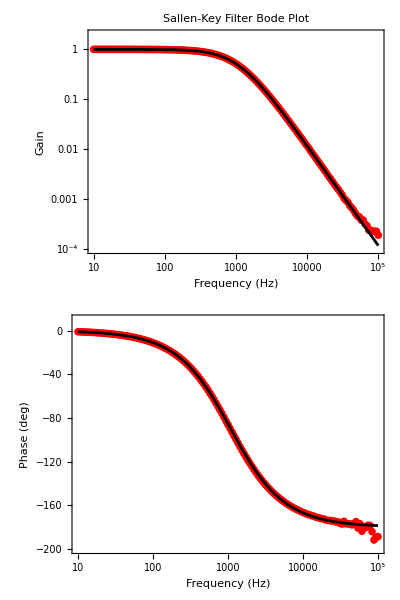

```mathematica
"■";
Column[
{Show[
ListLogLogPlot[{freq,gain}ᵀ,PlotRange->{{10, 100000},{0.0001,2}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600],
LogLogPlot[Abs[H[ⅈ f 2 π,αOpt,ωOpt 2 π,ζOpt]],{f,10,100000},PlotStyle->Black]],
Show[
ListLogLinearPlot[{freq,phase}ᵀ,PlotRange->{{10, 100000},{-200,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,αOpt,ωOpt 2 π,ζOpt]],{f,10,100000},PlotStyle->Black]]},
Spacings->0]
```

#### Parameter Sensitivity Functions

We can ask just how important each parameter is to the overall fit. Do we have parameters which can be varied over a wide range without having much effect on the “goodness of fit”?
Parameter sensitivity functions show us the effect of changing one parameter as the others are fixed at their optimal values. We will use the meanSSError function as we defined it above for this:

#### α Parameter Sensitivity Function

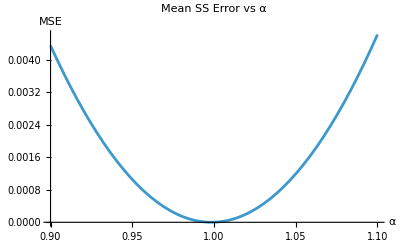

```mathematica
"■"; Plot[meanSSError[α,ωOpt 2 π,ζOpt],{α,0.9,1.1},PlotLabel->"Mean SS Error vs α",AxesLabel->{"α","MSE"},PlotRange->All]
```

We can see that the meanSSError is highly sensitive to the value of the static gain, α.

#### ω Parameter Sensitivity Function

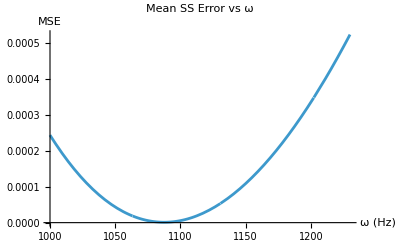

```mathematica
"■"; Plot[meanSSError[αOpt,ω 2 π,ζOpt],{ω,1000,1230},PlotLabel->"Mean SS Error vs ω",AxesLabel->{"ω (Hz)","MSE"},PlotRange->All]
```

We can see that the meanSSError is highly sensitive to the value of the natural frequency ω.

#### ζ Parameter Sensitivity Function

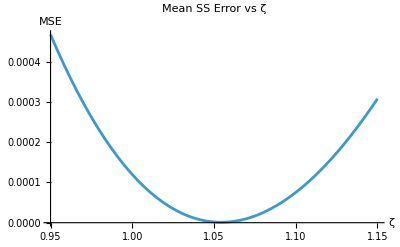

```mathematica
"■"; Plot[meanSSError[αOpt,ωOpt 2 π,ζ],{ζ,0.95,1.15},PlotLabel->"Mean SS Error vs ζ",AxesLabel->{"ζ","MSE"},PlotRange->All]
```

We can see that the meanSSError is highly sensitive to the value of the damping parameter ζ.

So we have found that all three parameters are important for our model. If one of them was basically a horizontal straight line then this would indicate that that parameter has no effect on the model and can be removed from the model or fixed at some arbitrary value.

#### Sallen -Key Filter

The second-order Sallen-Key filter has the following circuit:

-Graphics-

where Z1, Z2, Z3 and Z4 can each be any parallel or series combination of resistors, capacitors and inductors. By choosing what Z1, Z2, Z3, and Z4 are we can design a variety of second-order filters (low-pass, high-pass, band-pass and band-stop).

From https://upload.wikimedia.org/wikipedia/commons/e/e3/Sallen-Key_Generic _Circuit.svg

The general transfer function is:

```mathematica
tf[s_]:=(z3[s]z4[s])/(z1[s] z2[s] +z3[s](z1[s]+z2[s]) + z3[s] z4[s])
```

```mathematica
tf[s]
```

(z3[s] z4[s])/(z1[s] z2[s]+(z1[s]+z2[s]) z3[s]+z3[s] z4[s])

#### Low-pass Filter

For the case of a second-order, low-pass, filter we have:

-Graphics-

```mathematica
z1[s_]:=r1;
z2[s_]:=r2;
z3[s_]:=1/(c1 s);
z4[s_]:=1/(c2 s);
```

```mathematica
tf[s]//Factor
```

1/(1+c2 r1 s+c2 r2 s+c1 c2 r1 r2 s^2)

```mathematica
1/(1+c2 r1 s+c2 r2 s+c1 c2 r1 r2 s^2)//Simplify
```

1/(1+c2 s (r1+r2+c1 r1 r2 s))

```mathematica
(1/(c1 c2 r1 r2))/(s^2+(r1+r2)/(c1 r1 r2)s+1/(c1 c2 r1 r2))
```

1/(c1 c2 r1 r2 (1/(c1 c2 r1 r2)+((r1+r2) s)/(c1 r1 r2)+s^2))

Note that this is the form of a second-order, low-pass, transfer function

```mathematica
"■"; tf[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2)
```

where

```mathematica
"■"; α=1;
```

and

```mathematica
ω=√(1/(c1 c2 r1 r2))
```

√(1/(c1 c2 r1 r2))

and

```mathematica
ζ=(r1+r2)/(c1 r1 r2) 1/(2 √(1/(c1 c2 r1 r2)));
```

```mathematica
ζ=(r1+r2)/(c1 r1 r2)(√(c1 c2 r1 r2))/2;
```

For example if we want the second-order low pass filter to have unity damping (i.e., ζ = 1) and a cutoff frequency (i.e., ω) of around 1 kHz then we can set both resistors r1 = r2 = 10 kΩ and both capacitors c1 = c2 = 20 nF.

```mathematica
"■"; c1=c2=15.0 10^-9; 
r1=r2=1.0 10^4;
```

The natural frequency (cut-off frequency) will be:

```mathematica
"■"; ω=√(1/(c1 c2 r1 r2)) 1/(2π)  (* Hz *)
```

1061.03

And the damping parameter will be:

```mathematica
"■"; ζ=(r1+r2)/(c1 r1 r2)(√(c1 c2 r1 r2))/2
```

1.

Compare these α, ω, and ζ  values to those determined from the measured Sallen-Key filter response:

```mathematica
"■"; {α,ω,ζ}
```

{1,1061.03,1.}

and

```mathematica
"■"; {αα,ωω,ζζ}
```

{αα,ωω,ζζ}

These are amazingly close! 
The resistor values (10 kΩ) and capacitor values (15 nF) will not be exactly these values. Metal film resistors as used here are normally within around 1% and ceramic capacitors as used here are normally within 5%.

#### Predicting the Sallen-Filter response to any input

As detailed above the Sallen-Key transfer function is:

```mathematica
"■"; tf[s,α,ω 2π,ζ]
```

(4.44444×10^7)/(4.44444×10^7+13333.3 s+s^2)

Remember the transfer function requires the natural frequency to be specified in rad/s.

Now that we know the transfer function of the Sallen-Key filter we can predict its output for any input.

#### Sallen-Key filter Unit Step Response

We can determine the unit step response by multiplying the transfer function by 1/s and then inverse Laplace transforming:

```mathematica
"■"; step[t_]:=InverseLaplaceTransform[tf[s,α,ω 2π,ζ]/s,s,t]
```

```mathematica
"■"; step[t]
```

4.44444×10^7 (2.25×10^-8+ⅇ^(-6666.67 t) (-2.25×10^-8-0.00015 t))

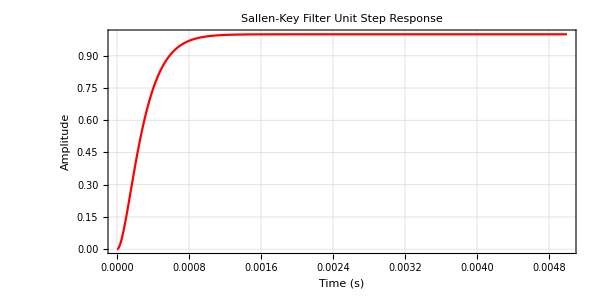

```mathematica
"■"; Plot[step[t],{t,0,0.005},PlotRange->All,
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Unit Step Response ",
FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.5,ImageSize->600]
```

Try subjecting the actual Sallen-Key filter to a 100 Hz square wave input (switching between 0 V and 1 V) and see if the square wave response is as predicted above. It should be bang on!

-Graphics-

-Graphics-

Note the rise time of about 1 ms. Compare this with the 1 ms rise time in our predicted step response above.

#### Measure the Step Response and Save

Acquire a single oscilloscope sweep (use Single rather than Run) and then Export (i.e., save) the step response as you did for the frequency response. Save to a .csv file on your Downloads folder called: Sallen-Key Filter Step Response

#### Import the Measured Step Response in to Mathematica

You will need to change the file name below to the location where you saved the measured step response.

```mathematica
"■";  
file=
"C:\Users\ariel\Downloads\Sallen-Key Filter Step Response ariel.csv";
data=Import[file,"Data"][[1;;31]]  (* header info *)
```

{{#Digilent WaveForms Oscilloscope Acquisition},{#Device Name: Discovery3},{#Serial Number: SN:210415BE8CFA},{#Date Time: 2026-03-17 19:19:37.203.783.500},{#Sample rate: 3.125e+06Hz},{#Samples: 16384},{#Trigger: Source: Channel 1 Type: Edge Condition: Rising Level: 380 mV Hyst.: Auto HoldOff: 0 s},{#Channel 1: Range: 200 mV/div Offset: -600 mV Sample Mode: Average},{#Channel 2: Range: 200 mV/div Offset: -600 mV Sample Mode: Average},{#Wavegen Channel 1: Running},{#Mode: Simple},{#Type: Square},{#Frequency: 100 Hz},{#Period: 10 ms},{#Amplitude: 500 mV},{#Offset: 500 mV},{#Symmetry: 50 %},{#Phase: 0 °},{#Power Supplies: ON},{#Positive Supply: ON},{#Voltage: 5 V Readback: 5.000170986 V},{#Negative Supply: ON},{#Voltage: -5 V Readback: -4.9977263891 V},{Time (s),Channel 1 (V),Channel 2 (V)},{-0.00262114,-0.000602982,0.00102129},{-0.00262082,-0.000446304,0.000864061},{-0.0026205,-0.000602982,0.000313753},{-0.00262018,-0.000916338,0.000392369},{-0.00261986,-0.000602982,0.00109991},{-0.00261954,-0.000289627,0.00070683},{-0.00261922,-0.000211288,0.0005496}}

Check first triplet of data (i.e., at 10 Hz) is at CSV row 25 (note that yours may be at another line number):

```mathematica
"■"; Import[file,"Data"][[25]]
```

{-0.00262114,-0.000602982,0.00102129}

```mathematica
"■"; data=Import[file,"Data"][[25;;All]] ;(* data starts at element 23 *)
n=Length[data]
```

16384

This length should be the same as the number of samples collected by WaveForms (e.g., 16,384).

```mathematica
"■"; time=data[[All,1]];
input=data[[All,2]];
output=data[[All,3]];
```

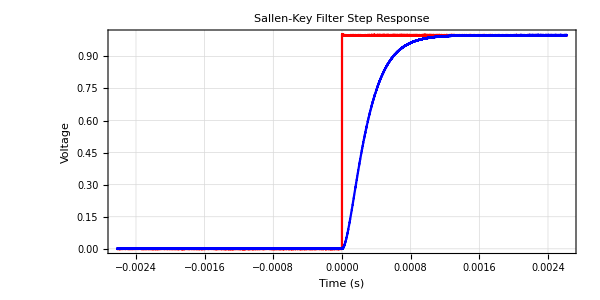

```mathematica
"■"; ListLinePlot[{{time,input}ᵀ,{time,output}ᵀ},PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Red,Blue},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Step Response",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

Now lets plot the measured step response together with our predicted step response:

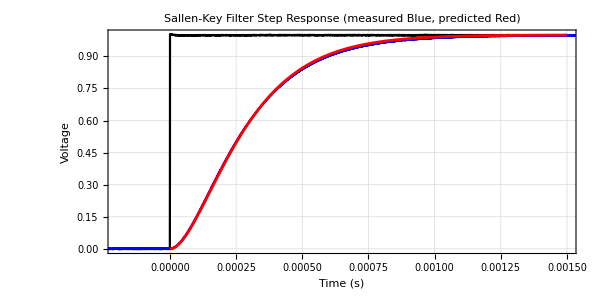

```mathematica
"■"; Show[
ListLinePlot[{{time,input}ᵀ,{time,output}ᵀ},PlotRange->{{-0.0002,0.0015},All},
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Black,Blue},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Step Response (measured Blue, predicted Red)",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600],
Plot[step[t],{t,0,0.0015},PlotStyle->Red]]
```

Clearly our prediction is almost bang-on.

#### Use the Sallen-Key filter to filter a signal

If you use the Waveform generator to generate a stochastic white noise signal (e.g., 2V amplitude, 200 kHz) which is fed to the input of the Sallen-Key filter you can feed the output to the Discovery 2 Spectrum Analyzer to see the effect of the low-pass filter (listen to the white noise input). Compare the spectrum of the input to that of the output.

-Graphics-

Note the settings of the Spectrum analyzer. We have used Exponential RMS filtering of the spectrum.

-Graphics-

Notice that the input power spectrum (blue) is flat to 100 kHz whereas the output power spectrum (red) rolls off beyond the “cut-off” frequency of around 1 kHz. In other words the Sallen-Key filter is low-pass filtering the signal as expected. 

Note that the output power spectrum high frequency roll-off slope is around -2 (on these log log co-ordinates). 
Note also the high frequency roll-off stops at around 30 kHz and then flattens out. This shows the noise floor of the filter. This noise floor is in part due to the limited resolution of the Digilent Discovery 3 ADCs and also due to the inherent noise in the Sallen-Key filter itself. However if our objective was to build a filter for filtering audio signals (for humans 20 Hz to 20 kHz hearing range) then the 30 kHz noise floor is perhaps acceptable.

#### Measure the Response to the Stochastic White Noise Input and Save

Use the Waveform generator to generate a stochastic white noise signal (e.g., 2 V amplitude, 10 kHz) and feed it to the input of the Sallen-Key filter.

-Graphics-

Record both this input (channel 1) and the resulting output (channel 2) on the Digilent Waveforms Scope using the settings shown in the figure below (note that the sweep starts at t=0). Acquire a single  oscilloscope sweep (use Single rather than Run) and then Export (i.e., save) both input and output signals. Save to a .csv file on your Downloads folder called: Sallen-Key Filter Stochastic Response

-Graphics-

#### Import the Measured Step Response in to Mathematica

You will need to change the file name below to the location where you saved the measured step response.

```mathematica
"■";  
file=
"C:\Users\ariel\Downloads\Sallen-Key Filter Stochastic Response ariel.csv";
data=Import[file,"Data"][[1;;31]]  (* header info *)
```

{{#Digilent WaveForms Oscilloscope Acquisition},{#Device Name: Discovery3},{#Serial Number: SN:210415BE8CFA},{#Date Time: 2026-03-17 19:23:40.534.606.930},{#Sample rate: 319489Hz},{#Samples: 16384},{#Trigger: Source: Channel 1 Type: Edge Condition: Rising Level: 380 mV Hyst.: Auto HoldOff: 0 s},{#Channel 1: Range: 500 mV/div Offset: 0 V Sample Mode: Average},{#Channel 2: Range: 500 mV/div Offset: 0 V Sample Mode: Average},{#Wavegen Channel 1: Running},{#Mode: Simple},{#Type: Noise},{#Frequency: 10 kHz},{#Period: 100 us},{#Amplitude: 2 V},{#Offset: 0 V},{#Power Supplies: ON},{#Positive Supply: ON},{#Voltage: 5 V Readback: 5.000170986 V},{#Negative Supply: ON},{#Voltage: -5 V Readback: -4.9977263891 V},{Time (s),Channel 1 (V),Channel 2 (V)},{-0.000640934,0.668311,0.764328},{-0.000637804,0.668389,0.767394},{-0.000634674,0.668311,0.769988},{-0.000631544,0.668232,0.772583},{-0.000628414,0.668468,0.77502},{-0.000625284,0.668468,0.776985},{-0.000622154,0.668468,0.779186},{-0.000619024,0.668389,0.781073},{-0.000615894,0.668311,0.78296}}

Check first triplet of data (i.e., at 10 Hz) is at CSV row 25 (note that yours may be at another line number):

```mathematica
"■"; Import[file,"Data"][[23]]
```

{-0.000640934,0.668311,0.764328}

```mathematica
"■"; data=Import[file,"Data"][[23;;All]] ;(* data starts at element 23 *)
n=Length[data]
```

16384

This length should be the same as the number of samples collected by WaveForms (e.g.,  2^14 = 16,384).

```mathematica
"■"; time=data[[All,1]];
x=data[[All,2]];
y=data[[All,3]];
```

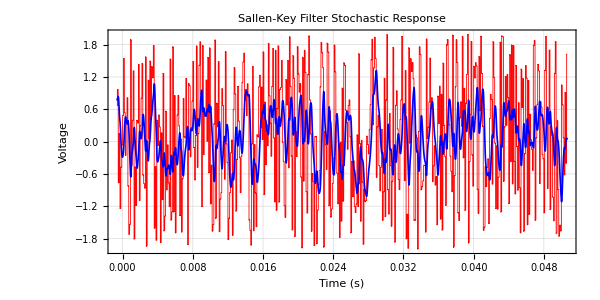

```mathematica
"■"; ListLinePlot[{{time,x}ᵀ,{time,y}ᵀ},PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{{Thickness[0.001],Red},{Thickness[0.002],Blue}},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

Lets zoom in:

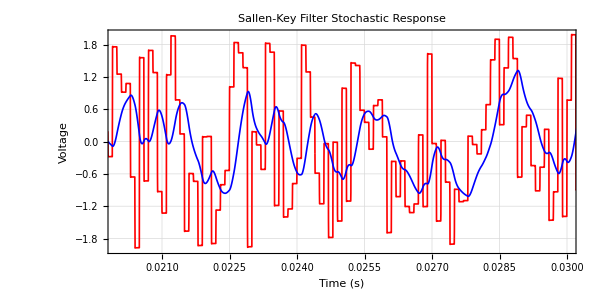

```mathematica
"■"; ListLinePlot[{{time,x}ᵀ,{time,y}ᵀ},PlotRange->{{0.02,0.03},All},
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{{Thickness[0.002],Red},{Thickness[0.002],Blue}},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

The time between samples is:

```mathematica
"■"; Δt=time[[2]]-time[[1]]
```

3.13×10^-6

The reciprocal of this is the sampling rate in Hz:

```mathematica
"■"; 1/Δt
```

319489.

#### Determine the System Impulse Response Function

We can inverse Laplace transform the Sallen-Key transfer function to get the system impulse response function as an equation:

```mathematica
"■"; InverseLaplaceTransform[tf[s,α,ω 2π,ζ],s,t]
```

4.44444×10^7 ⅇ^(-6666.67 t) t

Copy the equation you get on the previous line and paste it into the right side of the following equation:

```mathematica
"■"; h[t_]:=4.444444444444445*^7 ⅇ^(-6666.666666666666 t) t
```

It is customary to denote the system impulse response by h

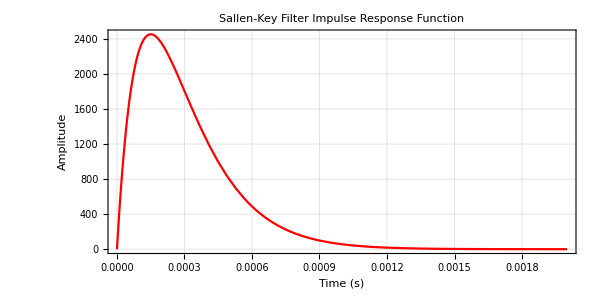

```mathematica
"■"; Plot[h[t],{t,0,0.002},PlotRange->All,
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Impulse Response Function",
FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.5,ImageSize->600]
```

We need to convert the symbolic impulse response function, h,  (sometimes called the parametric impulse response function) in to a sampled version (sometimes called a nonparametric impulse response function (i.e., a list of numbers)) which we denote hi :

```mathematica
"■"; τi=Range[0,0.002,Δt];
hi=h[τi];
```

Now lets plot the parametric and nonparametric second-order impulse response functions:

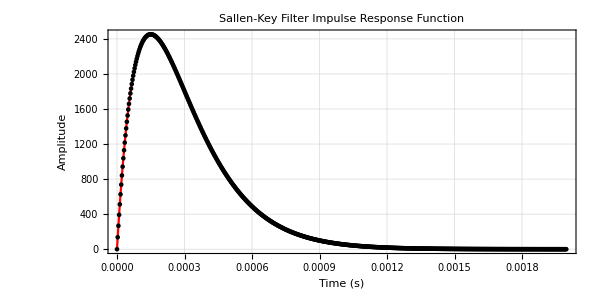

```mathematica
"■"; Show[
Plot[h[t],{t,0,0.002},PlotRange->All,
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Impulse Response Function",
FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.5,ImageSize->600],
ListPlot[{τi,hi}ᵀ,PlotStyle->Black]]
```

#### Convolve the Input with the Nonparametric Impulse Response Function

Now that we have the sampled impulse response function (i.e., the nonparametric impulse response function) we can numerically convolve it with the measured input to get a prediction of the output:

```mathematica
"■"; yp=Δt ListConvolve[hi,x,1];(* 1 tells the algorithm to make the input and output lengths the same *)
```

Now lets plot the measured step response together with our predicted step response:

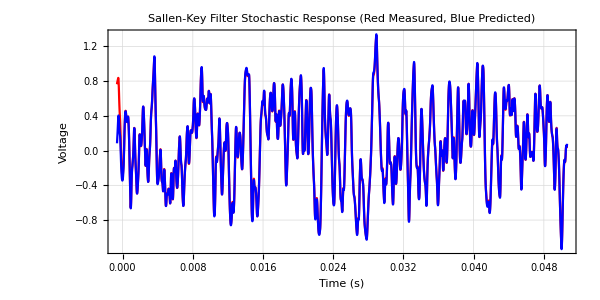

```mathematica
"■"; ListLinePlot[{{time,y}ᵀ,{time,yp}ᵀ},PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Red,Blue},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response (Red Measured, Blue Predicted)",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

#### Prediction Errors

We can subtract the measured output from the predicted output to give the prediction errors:

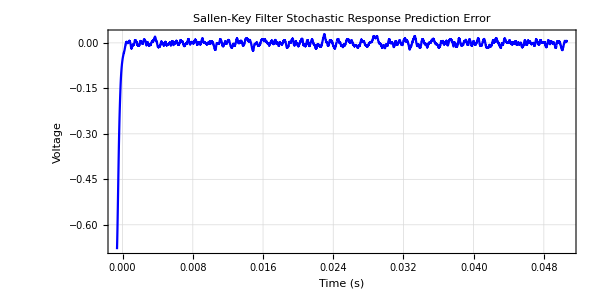

```mathematica
"■"; ListLinePlot[{time,(yp-y)}ᵀ,PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Red,Blue},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response Prediction Error",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

Notice that the largest error is at the start. This is very common and is caused by the convolution implicitly assuming that the input was 0 when t < 0. It is common to remove from the output prediction the first m values where m is the length of the nonparametric impulse response. Lets do this and re-plot:

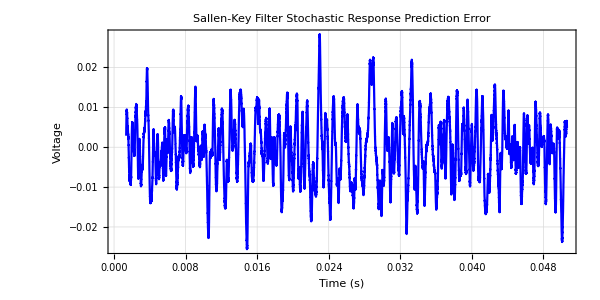

```mathematica
"■"; 
m=Length[hi];
ListLinePlot[{time[[m;;All]],(yp-y)[[m;;All]]}ᵀ,PlotRange->All,
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->{Red,Blue},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response Prediction Error",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

Lets plot this on the same voltage axis as on the original output plot:

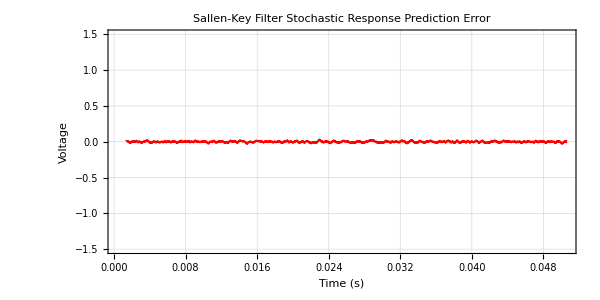

```mathematica
"■"; 
m=Length[hi];
ListLinePlot[{time[[m;;All]],(yp-y)[[m;;All]]}ᵀ,PlotRange->{All,{-1.5,1.5}},
PlotTheme->{"Scientific","Grid"},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Stochastic Response Prediction Error",
FrameLabel->{"Time (s)","Voltage"},AspectRatio->0.5,ImageSize->600]
```

This clearly shows just how small output prediction errors are.

#### % Variance Accounted For (%VAF)

It is useful to have a single measure of the degree to which our model (parametric or non-parametric) can predict the output for a given input. One such measure is the variance accounted for. It tells us the % of the output variation (variance) which is accounted for by the model. If every nuance in the output is predicted by a model then the %VAF = 100%. Conversely, if none of the output is predicted by the model the %VAF = 0. As a general rule we normally want to see the %VAF well above 75%. For example, if the %VAF = 80% then the 20% unaccounted for by the model is some combination of noise and nonlinearity (you can only find out how much is noise vs nonlinearity by doing a nonlinear analysis (e.g., nonlinear system ID).
The % VAF obtained here is:

```mathematica
"■"; vaf=100(1-Variance[(yp-y)[[m;;All]]]/Variance[y[[m;;All]]])
```

99.9684

So we have clearly shown that the first-order model successfully predicts output measured output.

#### Direct Estimation of the System Impulse Response Function

In the analysis above we experimentally determined the Sallen-Key filter frequency response (Bode plot) by sweeping an input sinusoid from 10 Hz to 100 kHz. We then fitted a second-order transfer function to it using nonlinear least squares. We then inverse Laplace transformed this transfer function to get the second-order parametric impulse response function. We then ran another experiment in which a 10 kHz stochastic white, uniformly distributed, signal was used as the Sallen-Key filter input while the output was measured.  We then sampled the parametric impulse response function at the same sampling rate as used in the stochastic input experiment and used the resulting non-parametric second-order impulse function to predict the output via numeric convolution. This was a fairly arduous sequence of operations. Furthermore the swept sin wave experiment took 10’s of seconds whereas the stochastic input output measurement only took 50 ms!

We now ask it is possible to determine the Sallen-Key filter impulse response function directly from the stochastic input and output measurements.  The answer is yes and we will show how it can be done in subsequent notes.

#### Code to enable single mouse click evaluation of code

```mathematica
Button["■",SelectionMove[EvaluationCell[],All,TextLine];
SelectionEvaluate[EvaluationNotebook[]],Appearance->"Frameless"]
```

■